## Day 13: A Maze of Twisty Little Cubicles

### Part 1:

```mathematica
IsWall[{x_,y_},f_]:=If[(x<0)||(y<0),True,OddQ@Length@Select[IntegerDigits[x*x+3*x+2*x*y+y+y*y+f,2],#==1&]]
IsOpen[{x_,y_},f_]:=!IsWall[{x,y},f]
```

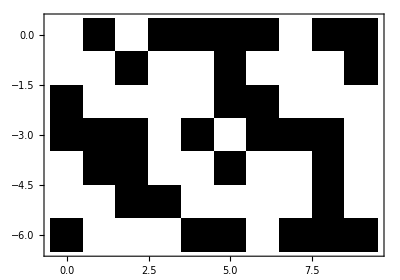

```mathematica
testfav=10;
Graphics[
Table[{If[IsWall[{i,j},testfav],Black,White],Rectangle[{i-0.5,-j-0.5}]},{i,0,9},{j,0,6}],Frame->True]
```

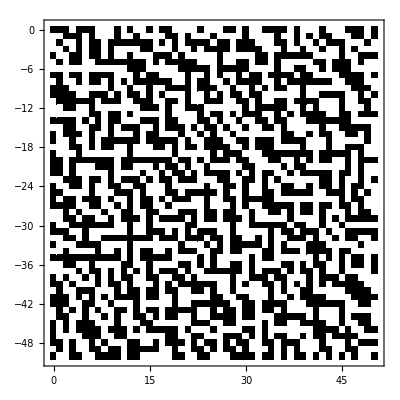

```mathematica
fav=1364;
mazeGraphics=Graphics[
Table[{If[IsWall[{i,j},fav],Black,White],Rectangle[{i-0.5,-j-0.5}]},{i,0,50},{j,0,50}],Frame->True]
```

```mathematica
createEdges[{x_,y_},f_]:=Module[{edges={}},
If[IsOpen[{x,y},f],
If[IsOpen[{x+1,y},f],AppendTo[edges,{x,y}<->{x+1,y}]];
(*If[IsOpen[{x-1,y},f],AppendTo[edges,{x,y}<->{x-1,y}]];
If[IsOpen[{x,y-1},f],AppendTo[edges,{x,y}<->{x,y-1}]];*)
If[IsOpen[{x,y+1},f],AppendTo[edges,{x,y}<->{x,y+1}]];
];
edges
]
```

```mathematica
createGraph[fav_,m_,n_]:=Module[{graph,vc},
graph=Flatten@Table[createEdges[{i,j},fav],{i,0,m},{j,0,n}];
vc={#[[1]],-#[[2]]}&/@VertexList[graph];
Graph[graph,VertexCoordinates->vc]
]
```

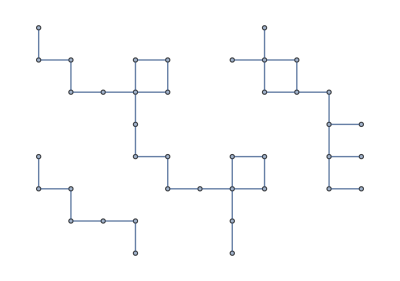

```mathematica
testG=createGraph[testfav,9,6]
```

```mathematica
ShortestRoute[g_,start_,end_]:=Module[{path,steps,hl},
path=FindShortestPath[g,start,end];
steps=Length@path-1;
hl=#[[1]]<->#[[2]]&/@Partition[path,2,1];
Column[{Row[{"Steps: ",steps}],HighlightGraph[g,hl,ImageSize->500]}]
]
```

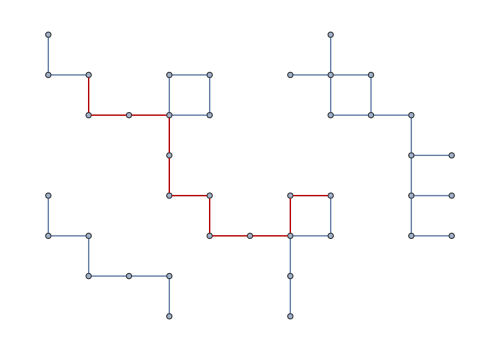
Steps: 11
-Graphics-

```mathematica
ShortestRoute[testG,{1,1},{7,4}]
```

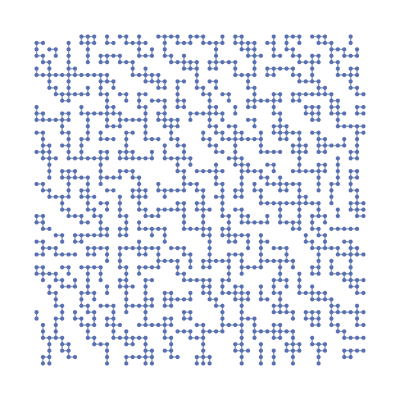

```mathematica
G=createGraph[fav,50,50]
```

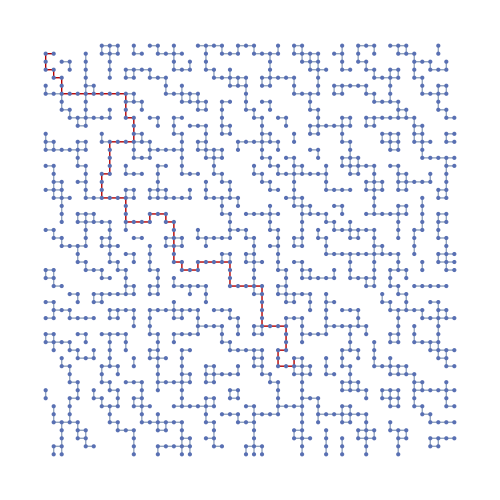
Steps: 86
-Graphics-

```mathematica
ShortestRoute[G,{1,1},{31,39}]
```

Correct :)

### Part 2:

```mathematica
dist=Select[GraphDistance[G,{1,1}],#≤50&]
```

{1,0,2,3,4,11,10,9,49,48,47,47,46,5,6,8,45,7,9,9,10,11,44,10,12,13,43,11,14,14,15,44,45,44,42,41,40,39,38,16,15,14,13,12,13,12,12,13,15,39,37,36,35,13,16,34,14,17,28,27,26,31,30,32,33,35,15,18,25,27,28,29,36,16,24,37,17,17,18,18,19,20,23,38,39,38,38,39,40,41,41,19,21,22,23,24,24,25,26,42,20,25,27,43,26,27,44,45,28,46,29,47,48,50,35,36,34,33,32,30,49,31,31,32,33,34,35}

```mathematica
dist//Length
```

127